```mathematica
ClearAll["Global`*"];
m=1000;
g = 9.81;
Fop=k*v^2;
vPocz = 25;
Fpos = Fc * μ;
Fc = m * g;
s = Integrate[v, t];
Fhamowania = Fop + Fpos;
decel  = -Fhamowania / m;
v = Max[vPocz + Integrate[decel, {t, 0 ,t}] ,0];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

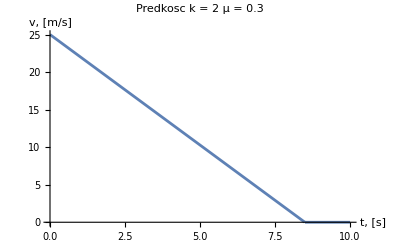

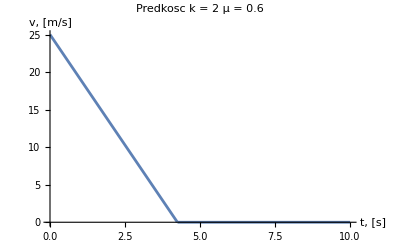

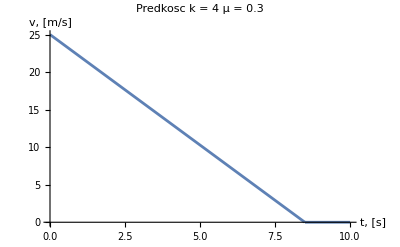

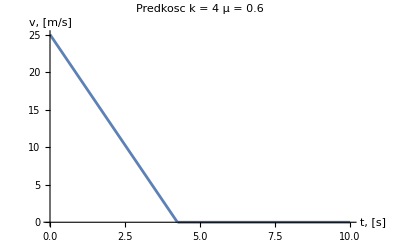

```mathematica
k := 2;
μ =0.3;
Plot[v, {t, 0 ,10},AxesLabel->{"t, [s]","v, [m/s]"},PlotLabel->"Predkosc k = 2    μ = 0.3"]
k := 2;
μ :=0.6;
Plot[v, {t, 0 ,10},AxesLabel->{"t, [s]","v, [m/s]"},PlotLabel->"Predkosc k = 2    μ = 0.6"]

k := 4;
μ :=0.3;
Plot[v, {t, 0 ,10},AxesLabel->{"t, [s]","v, [m/s]"},PlotLabel->"Predkosc k = 4    μ = 0.3"]


k := 4;
μ :=0.6;
Plot[v, {t, 0 ,10},AxesLabel->{"t, [s]","v, [m/s]"},PlotLabel->"Predkosc k = 4    μ = 0.6"]
```